```mathematica
Clear["Global`*"];
f = 1/4/π/D/τ*Exp[-(x^2+y^2)/4/D/τ]
```

(ⅇ^((-x^2-y^2)/(4 D τ)))/(4 D π τ)

```mathematica
J = Assuming[D≥0&&T≥0, 1/T*Integrate[r^3/2/D/τ*Exp[-r^2/4/D/τ],{r,0,∞},{τ,0,T}]]
```

2 D T

```mathematica
J = Assuming[D>0&&T>0, 1/T*Integrate[(x^2+y^2)*f,{x,-∞,∞},{y,-∞,∞},{τ,0,T}]]
```

2 D T

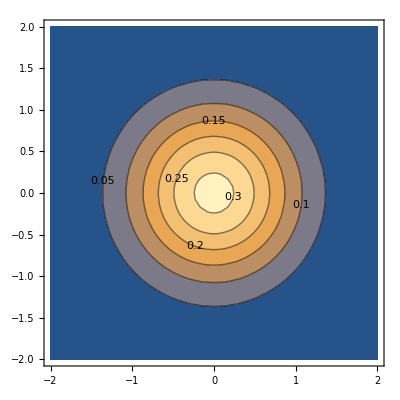

```mathematica
ContourPlot[f/.{τ->10,D-> 0.025},{x,-2,2},{y,-2,2},ContourLabels->True]
```